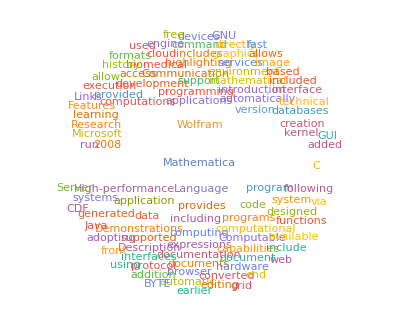

```mathematica
WordCloud[WikipediaData["Mathematica"]]
```

```mathematica
Crash Course in Mathematica for Graduate Students
```

## Introduction Lesson 2

In the previous lesson we played with calculus but MATHEMATICA is good also for doing linear algebra calculations which are common in physics.
We can define vector of elements simply doing

```mathematica
v= {1, 3, 5}
w = {2, 4, 6}
v+w
```

{1,3,5}

{2,4,6}

{3,7,11}

And also matrices

```mathematica
M = {{1, 3, 5}, {2, 5, 8}, {1, 4, 9}}//MatrixForm (*gives the Matrix-like output*)
```

(1 | 3 | 5
2 | 5 | 8
1 | 4 | 9)

Obviously all the standard operation between vector and matrices are allowed,  but only in the ‘original version’.

```mathematica
v={1, 2, 3}//MatrixForm
M.v
```

(1
2
3)

(1 | 3 | 5
2 | 5 | 8
1 | 4 | 9).(1
2
3)

```mathematica
M = {{1, 3, 5}, {2, 5, 8}, {1, 4, 9}};
v={1, 2, 3}
M.v
M.v//MatrixForm
```

{1,2,3}

{22,36,36}

(22
36
36)

Matrices and vectors are lists for MATHEMATICA. We have access to their elements simply

```mathematica
M[[1]] (*first row*)
```

{1,3,5}

```mathematica
M[[1, 3]](*first row but also third column*)
M[[1]][[ 3]](*but the meaning of this is slightly different*)
```

5

5

```mathematica
M[[All , 3]](*only the third column*)
```

{5,8,9}

Lists are more general object. For more info see [4].

## Current in DC Circuit

Consider the DC circuit in the picture above. Use Kirchoff’s Laws to determine the currents i_1, i_2 and i_3 in terms of V, R_1, R_2 and R_3.
Kirchoff’s node and loops lwas give us the following equations:

Write these four equations and solve for the three currents using Solve.

Now define the matrix related to this linear system. Find the three currents again using LinearSolve.

## Special Relativity and Boosted Objects

If we define the Lorentzian metric as the matrix

```mathematica
g=DiagonalMatrix[{1, -1, -1, -1}];
%//MatrixForm
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

we can use it to compute scalar product in Minkowski space.

```mathematica
v1= {1, 0, 0, 1};
v2={1, 0, 0, -1};
v2.g.v1 (*this is the same than the Dot[] function*)
```

2

Consider a pion ( π ) at rest which decays into two photons ( γ ).  In the rest frame of the pion the μ and the ν will decay in a back-to-back configuration.

Define the 4-vectors of the particles in the rest frame. Find the angle between the μ and the ν.

Define a boost matrix and compute how the angle between the two photons varies in a generic boosted frame in the x directions. Plot θ(β). How you expect it varies with β?

## Inertia Tensor and Principal Axes

The most general notion of moment of inertia is encoded in the inertia tensor.

Measured in the body frame  is a constant real symmetric matrix, hence it admits a decomposition into a rotation matrix  and a diagonal matrix  such that

Columns of the rotation matrix  define the directions of the principal axes of the body. If  the scalar  and  are called principal moments of inertia.
Given the mass distribution below compute the inertia tensor for this body and find its principal axes/moments.

```mathematica
Ω=Cylinder[{{0,0,0},{1,1,1}},1/2]; (*A cylinder from the origin to {1,1,1} with radius 1/2:*)
Graphics3D[Ω]
```

-Graphics3D-

Calculate the volume and the center of mass of the object.

Calculate the inertia tensor using the formula

```mathematica
I=∫∫∫_Vol ρ(x, y, z)(|r|^2 Subscript[id, 3]-r⊗r)dx dy dz
```

Compare this result with the output of MomentOfInertia.

Find principal axes and momenta of inertia using eigenvectors and eigenvalues of this matrix.

## Eigenmodes of the Heat Equation

The Heat Equation is

Using the DEigensystem function find heat equation first 20 eigenfunctions and eigenvalues.

Plot them. How they behaves for late time?

```mathematica
(*It is possible to decompose an arbitrary function on the eigenfunction base and study the evolution of the system with this as an initial condition?*)
```

Consider the following temperature profile as the initial condition. How does the system evolve?

```mathematica
Code Here
```

```mathematica
L2norm[f1_, f2_, Domain_:{x, 0, 1}]:=Module[{},
Integrate[Conjugate[f2]*f1, Domain]
]
```

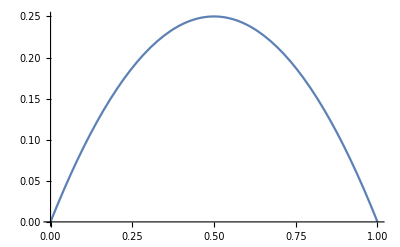

```mathematica
f[x_]=x(1-x); (*our function*)
Plot[%, {x, 0, 1}]
```

## References

[1] A Mathematica Primer for Physicists, Jim Napolitano
[2] https://reference.wolfram.com/language/tutorial/KeyboardShortcutListing.html
[3] https://mathematica.stackexchange.com/questions/18393/what-are-the-most-common-pitfalls-awaiting-new-users/25616#25616
[4] https://reference.wolfram.com/language/tutorial/Lists.html#2534
[5] https://demonstrations.wolfram.com/2DWavePropagation/
[6] https://mathematica.stackexchange.com/questions/134609/why-should-i-avoid-the-for-loop-in-mathematica
[7] https://reference.wolfram.com/language/ref/Module.html